# Infinite 3D medium, Isotropic Point Source, Isotropic Scattering

## Cauchy Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3DisopointIsoscatterCauchy`"]
```

inf3DisopointIsoscatterCauchy`

## Analytical results

```mathematica
pc[s_]:=2/(Pi(1+s^2))
```

### Collision rate density

collision rate density Cc due to correlated emission:

#### derivation

```mathematica
Clear[cpc,c];
cpc[s_]:=c 2/(Pi(1+s^2))
```

```mathematica
f00=Fpc[0,0,cpc,u];
```

```mathematica
o=1;
Clear[A,b,c,r,h,F];
A[n_]:=0;
A[0]:=1;
A[1]:=0;
A[2]:=0;
hsystem=Table[h[k]==2/Pi u F[k,0]+ Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.F[0,0]->f00/.F[0,1]->-f10/.F[1,1]->f11/.F[1,0]->f10/.F[2,0]->f20/.F[0,2]->f20/.F[2,2]->f22]
```

{{h[0]→-(2 c u (-1+Cosh[u]-Sinh[u]))/(π (-c+u+c Cosh[u]-c Sinh[u]))}}

```mathematica
Clear[r,c];(2k+1)1/(4 Pi c)(h[k])u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify
```

{((-1+ⅇ^u) u^2 Sinc[r u])/(2 π^2 (c-c ⅇ^u+ⅇ^u u))}

#### result

```mathematica
Ccexact[r_,c_]:=NIntegrate[((-1+ⅇ^u) u^2 Sinc[r u])/(2 π^2 (c-c ⅇ^u+ⅇ^u u)),{u,0,Infinity},Method->"ExtrapolatingOscillatory"]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_isotropicscatter_cauchy*"];
```

```mathematica
index[x_]:=Module[{data,c},
data=Import[x,"Table"];
c=data[[2,3]];
{c,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
numcollorders=simulations[[1]][[-1]][[2,13]];
```

## Compare analytic and MC

### Collision-rate density - Exact solution - comparison to MC

```mathematica
{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]}
```

{Set c,}

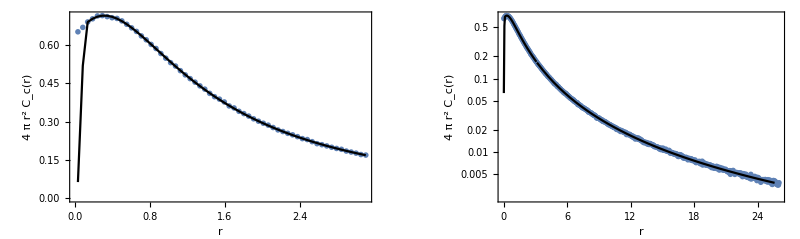

```mathematica
data=SelectFirst[simulations,#[[1]]==c&][[2]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->Black],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True,PlotStyle->Black],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->Black],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, Isotropic scattering, Cauchy random flight - correlated emission\nCollision-rate density C_c[r], c = "<>ToString[c]]
```

## Namespace

```mathematica
End[]
```

inf3DisopointIsoscatterCauchy`